## Análise de Dados

Entrada de Dados

Ajuste de Funções

Salvando Dados

Trabalhando com Imagens

◀     |     ▶

## Entrada de Dados

O comando chave do Mathematica para ler dados é o Import

```mathematica
lis=Import["http://www.ai.com.br/pessoal/indices/IBOVESPA.HTM"]
```

I B O V E S P A (posição final de mês)

PONTUAÇÃO E VARIAÇÃO PERCENTUAL

dez/93 => 003755
jan/94 => 007406 = 97,23%
fev/94 => 010538 = 42,29%
mar/94 => 015155 = 43,81%
abr/94 => 017084 = 12,73%
mai/94 => 024672 = 44,42%
jun/94 => 036231 = 46,85%
jul/94 => 042013 = 15,96%
ago/94 => 053294 = 26,85%
set/94 => 054840 = 2,90%
out/94 => 047979 = -12,51%
nov/94 => 046560 = -2,96%
dez/94 => 043539 = -6,49%
jan/95 => 038850 = -10,77%
fev/95 => 032708 = -15,81%
mar/95 => 029789 = -8,92%
abr/95 => 038137 = 28,02%
mai/95 => 037205 = -2,44%
jun/95 => 036033 = -3,15%
jul/95 => 038774 = 7,61%
ago/95 => 043105 = 11,17%
set/95 => 046701 = 8,34%
out/95 => 041283 = -11,60%
nov/95 => 043785 = 6,06%
dez/95 => 042990 = -1,82%
jan/96 => 051515 = 19,83%
fev/96 => 049577 = -3,76%
mar/96 => 049549 = -0,06%
abr/96 => 051641 = 4,22%
mai/96 => 057279 = 10,92%
jun/96 => 060438 = 5,52%
jul/96 => 061232 = 1,31%
ago/96 => 062594 = 2,22%
set/96 => 064468 = 2,99%
out/96 => 065331 = 1,34%
nov/96 => 066660 = 2,03%
dez/96 => 070399 = 5,61%
jan/97 => 079646 = 13,14%
fev/97 => 088287 = 10,85%
mar/97 => 090440 = 2,44%
abr/97 => 099820 = 10,37%
mai/97 => 113440 = 13,64%
jun/97 => 125670 = 10,78%
jul/97 => 128720 = 2,43%
ago/97 => 106090 = -17,58%
set/97 => 117970 = 11,20%
out/97 => 089860 = -23,83%
nov/97 => 093940 = 4,54%
dez/97 => 101960 = 8,54%
jan/98 => 097200 = -4,67%
fev/98 => 105700 = 8,74%
mar/98 => 119460 = 13,02%
abr/98 => 116770 = -2,25%
mai/98 => 098460 = -15,68%
jun/98 => 096780 = -1,71%
jul/98 => 107070 = 10,63%
ago/98 => 064720 = -39,55%
set/98 => 065930 = 1,87%
out/98 => 070470 = 6,89%
nov/98 => 086310 = 22,48%
dez/98 => 067840 = -21,40%
jan/99 => 081710 = 20,45%
fev/99 => 089100 = 9,04%
mar/99 => 106960 = 20,04%
abr/99 => 113500 = 6,11%
mai/99 => 110890 = -2,30%
jun/99 => 116260 = 4,84%
jul/99 => 104410 = -10,19%
ago/99 => 105640 = 1,18%
set/99 => 111060 = 5,13%
out/99 => 117000 = 5,35%
nov/99 => 137780 = 17,76%
dez/99 => 170910 = 24,05%
jan/00 => 163880 = -4,11%
fev/00 => 176600 = 7,76%
mar/00 => 178200 = 0,91%
abr/00 => 155370 = -12,81%
mai/00 => 149560 = -3,74%
jun/00 => 167270 = 11,84%
jul/00 => 164544 = -1,63%
ago/00 => 173460 = 5,42%
set/00 => 159280 = -8,17%
out/00 => 148670 = -6,66%
nov/00 => 132870 = -10,63%
dez/00 => 152590 = 14,84%
jan/01 => 176720 = 15,81%
fev/01 => 158940 = -10,06%
mar/01 => 144380 = -9,16%
abr/01 => 149180 = 3,32%
mai/01 => 146500 = -1,80%
jun/01 => 145600 = -0,61%
jul/01 => 137540 = -5,54%
ago/01 => 128410 = -6,64%
set/01 => 106360 = -17,17%
out/01 => 113640 = 6,85%
nov/01 => 129310 = 13,79%
dez/01 => 135770 = 5,00%
jan/02 => 127210 = -6,30%
fev/02 => 140330 = 10,31%
mar/02 => 132550 = -5,54%
abr/02 => 130850 = -1,28%
mai/02 => 128610 = -1,71%
jun/02 => 111390 = -13,39%
jul/02 => 097630 = -12,35%
ago/02 => 103820 = 6,34%
set/02 => 086230 = -16,94%
out/02 => 101680 = 17,92%
nov/02 => 105090 = 3,35%
dez/02 => 112680 = 7,22%
jan/03 => 109410 = -2,90%
fev/03 => 102810 = -6,03%
mar/03 => 112740 = 9,66%
abr/03 => 125570 = 11,38%
mai/03 => 134220 = 6,89%
jun/03 => 129730 = -3,34%
jul/03 => 135720 = 4,62%
ago/03 => 151740 = 11,80%
set/03 => 160110 = 5,52%
out/03 => 179820 = 12,31%
nov/03 => 201840 = 12,25%
dez/03 => 222360 = 10,17%
jan/04 => 218510 = -1,73%
fev/04 => 217550 = -0,44%
mar/04 => 221422 = 1,78%
abr/04 => 196072 = -11,45%
mai/04 => 195446 = -0,32%
jun/04 => 211489 = 8,21%
jul/04 => 223369 = 5,62%
ago/04 => 228032 = 2,09%
set/04 => 232452 = 1,94%
out/04 => 230522 = -0,83%
nov/04 => 251283 = 9,01%
dez/04 => 261962 = 4,25%
jan/05 => 243506 = -7,04%
fev/05 => 281391 =15,56%
mar/05 => 266100 = -5,43%
abr/05 => 248420 = -6,64%
mai/05 => 252070 = 1,47%
jun/05 => 250510 = -0,62%
jul/05 => 260420 = 3,96%
ago/05 => 280440 = 7,69%
set/05 => 315830 =12,62%
out/05 => 301930 = -4,40%
nov/05 => 319170 = 5,71%
dez/05 => 334550 = 4,82%
jan/06 => 383820 =14,73%
fev/06 => 386100 = 0,59%
mar/06 => 379520 = -1,71%

Fonte: Valor Econômico e Gazeta Mercantil

Principais Bolsas no Mundo
Brasil

Bolsa de Valores de São Paulo - BOVESPA
Bolsa de Valores do Rio de Janeiro - BVRJ
BM - Bolsa de Mercadorias & Futuros
Bolsa de Valores Bahia, Sergipe e Alagoas
Bolsa de Valores Extremo Sul
Bolsa de Valores do Paraná
SOMA - Sociedade Operadora do Mercado de Ativos S/A

E.U.A./Canadá

New York Stock Exchange - NYSE
American Stock Exchange - AMEX
NASDAQ
Toronto Stock Exchange
Alberta Stock Exchange
Arizona Stock Exchange
Boston Stock Exchange
Cincinnati Stock Exchange
Chicago Stock Exchange
Montreal Stock Exchange
Philadelphia Stock Exchange
Pacific Exchange
Vancouver Stock Exchange
Winnipeg Stock Exchange

América Latina

Bolsa de Comércio de Buenos Aires
Bolsa Mexicana de Valores
Bolsa Boliviana de Valores
Bolsa de Bogotá
Bolsa de Comércio de Santiago
Bolsa de Valores de Guayaquil
Bolsa de Valores de Lima
Caracas Stock Exchange

Europa

London Stock Exchange
Frankfurt Stock Exchange - Deutsche Boerse
Paris Stock Exchange
Swiss Exchange - SWX
Italian Stock Exchange
EASDAQ
Amsterdam Stock Exchange
Athens Stock Exchange
Bolsa de Barcelona
Bolsa de Madrid
Bolsa de Valores de Lisboa
Brussels Exchanges
Copenhagen Stock Exchange
Helsinki Stock Exchange.
Istanbul Stock Exchange
Prague Stock Exchange
Oslo Stock Exchange
Stockholm Stock Exchange
Warsaw Stock Exchange
Zagreb Stock Exchange

Ásia, África e Oceania

Tokyo Stock Exchange
Hong Kong Stock Exchange
Australian Stock Exchange
Johannesburg Stock Exchange
Korea Stock Exchange
Nagoya Stock Exchange
Osaka Stock Exchange
SAFEX - The South African Futures Exchange
Singapore Stock Exchange
Tel Aviv Stock Exchange
Thailand Stock Exchange

```mathematica
lis2=StringSplit[StringTake[lis,{75,-1684}],{"=>","=","\n"}]
```

{dez/93 , 003755,jan/94 , 007406 , 97,23%,fev/94 , 010538 , 42,29%,mar/94 , 015155 , 43,81%,abr/94 , 017084 , 12,73%,mai/94 , 024672 , 44,42%,jun/94 , 036231 , 46,85%,jul/94 , 042013 , 15,96%,ago/94 , 053294 , 26,85%,set/94 , 054840 , 2,90%,out/94 , 047979 , -12,51%,nov/94 , 046560 , -2,96%,dez/94 , 043539 , -6,49%,jan/95 , 038850 , -10,77%,fev/95 , 032708 , -15,81%,mar/95 , 029789 , -8,92%,abr/95 , 038137 , 28,02%,mai/95 , 037205 , -2,44%,jun/95 , 036033 , -3,15%,jul/95 , 038774 , 7,61%,ago/95 , 043105 , 11,17%,set/95 , 046701 , 8,34%,out/95 , 041283 , -11,60%,nov/95 , 043785 , 6,06%,dez/95 , 042990 , -1,82%,jan/96 , 051515 , 19,83%,fev/96 , 049577 , -3,76%,mar/96 , 049549 , -0,06%,abr/96 , 051641 , 4,22%,mai/96 , 057279 , 10,92%,jun/96 , 060438 , 5,52%,jul/96 , 061232 , 1,31%,ago/96 , 062594 , 2,22%,set/96 , 064468 , 2,99%,out/96 , 065331 , 1,34%,nov/96 , 066660 , 2,03%,dez/96 , 070399 , 5,61%,jan/97 , 079646 , 13,14%,fev/97 , 088287 , 10,85%,mar/97 , 090440 , 2,44%,abr/97 , 099820 , 10,37%,mai/97 , 113440 , 13,64%,jun/97 , 125670 , 10,78%,jul/97 , 128720 , 2,43%,ago/97 , 106090 , -17,58%,set/97 , 117970 , 11,20%,out/97 , 089860 , -23,83%,nov/97 , 093940 , 4,54%,dez/97 , 101960 , 8,54%,jan/98 , 097200 , -4,67%,fev/98 , 105700 , 8,74%,mar/98 , 119460 , 13,02%,abr/98 , 116770 , -2,25%,mai/98 , 098460 , -15,68%,jun/98 , 096780 , -1,71%,jul/98 , 107070 , 10,63%,ago/98 , 064720 , -39,55%,set/98 , 065930 , 1,87%,out/98 , 070470 , 6,89%,nov/98 , 086310 , 22,48%,dez/98 , 067840 , -21,40%,jan/99 , 081710 , 20,45%,fev/99 , 089100 , 9,04%,mar/99 , 106960 , 20,04%,abr/99 , 113500 , 6,11%,mai/99 , 110890 , -2,30%,jun/99 , 116260 , 4,84%,jul/99 , 104410 , -10,19%,ago/99 , 105640 , 1,18%,set/99 , 111060 , 5,13%,out/99 , 117000 , 5,35%,nov/99 , 137780 , 17,76%,dez/99 , 170910 , 24,05%,jan/00 , 163880 , -4,11%,fev/00 , 176600 , 7,76%,mar/00 , 178200 , 0,91%,abr/00 , 155370 , -12,81%,mai/00 , 149560 , -3,74%,jun/00 , 167270 , 11,84%,jul/00 , 164544 , -1,63%,ago/00 , 173460 , 5,42%,set/00 , 159280 , -8,17%,out/00 , 148670 , -6,66%,nov/00 , 132870 , -10,63%,dez/00 , 152590 , 14,84%,jan/01 , 176720 , 15,81%,fev/01 , 158940 , -10,06%,mar/01 , 144380 , -9,16%,abr/01 , 149180 , 3,32%,mai/01 , 146500 , -1,80%,jun/01 , 145600 , -0,61%,jul/01 , 137540 , -5,54%,ago/01 , 128410 , -6,64%,set/01 , 106360 , -17,17%,out/01 , 113640 , 6,85%,nov/01 , 129310 , 13,79%,dez/01 , 135770 , 5,00%,jan/02 , 127210 , -6,30%,fev/02 , 140330 , 10,31%,mar/02 , 132550 , -5,54%,abr/02 , 130850 , -1,28%,mai/02 , 128610 , -1,71%,jun/02 , 111390 , -13,39%,jul/02 , 097630 , -12,35%,ago/02 , 103820 , 6,34%,set/02 , 086230 , -16,94%,out/02 , 101680 , 17,92%,nov/02 , 105090 , 3,35%,dez/02 , 112680 , 7,22%,jan/03 , 109410 , -2,90%,fev/03 , 102810 , -6,03%,mar/03 , 112740 , 9,66%,abr/03 , 125570 , 11,38%,mai/03 , 134220 , 6,89%,jun/03 , 129730 , -3,34%,jul/03 , 135720 , 4,62%,ago/03 , 151740 , 11,80%,set/03 , 160110 , 5,52%,out/03 , 179820 , 12,31%,nov/03 , 201840 , 12,25%,dez/03 , 222360 , 10,17%,jan/04 , 218510 , -1,73%,fev/04 , 217550 , -0,44%,mar/04 , 221422 , 1,78%,abr/04 , 196072 , -11,45%,mai/04 , 195446 , -0,32%,jun/04 , 211489 , 8,21%,jul/04 , 223369 , 5,62%,ago/04 , 228032 , 2,09%,set/04 , 232452 , 1,94%,out/04 , 230522 , -0,83%,nov/04 , 251283 , 9,01%,dez/04 , 261962 , 4,25%,jan/05 , 243506 , -7,04%,fev/05 , 281391 ,15,56%,mar/05 , 266100 , -5,43%,abr/05 , 248420 , -6,64%,mai/05 , 252070 , 1,47%,jun/05 , 250510 , -0,62%,jul/05 , 260420 , 3,96%,ago/05 , 280440 , 7,69%,set/05 , 315830 ,12,62%,out/05 , 301930 , -4,40%,nov/05 , 319170 , 5,71%,dez/05 , 334550 , 4,82%,jan/06 , 383820 ,14,73%,fev/06 , 386100 , 0,59%,mar/06 , 379520 , -1,71%}

```mathematica
lis3=Partition[Delete[Delete[lis2,1],1],3];
```

```mathematica
lis4=lis3/.{x_,y_,z_}->y
```

{ 007406 , 010538 , 015155 , 017084 , 024672 , 036231 , 042013 , 053294 , 054840 , 047979 , 046560 , 043539 , 038850 , 032708 , 029789 , 038137 , 037205 , 036033 , 038774 , 043105 , 046701 , 041283 , 043785 , 042990 , 051515 , 049577 , 049549 , 051641 , 057279 , 060438 , 061232 , 062594 , 064468 , 065331 , 066660 , 070399 , 079646 , 088287 , 090440 , 099820 , 113440 , 125670 , 128720 , 106090 , 117970 , 089860 , 093940 , 101960 , 097200 , 105700 , 119460 , 116770 , 098460 , 096780 , 107070 , 064720 , 065930 , 070470 , 086310 , 067840 , 081710 , 089100 , 106960 , 113500 , 110890 , 116260 , 104410 , 105640 , 111060 , 117000 , 137780 , 170910 , 163880 , 176600 , 178200 , 155370 , 149560 , 167270 , 164544 , 173460 , 159280 , 148670 , 132870 , 152590 , 176720 , 158940 , 144380 , 149180 , 146500 , 145600 , 137540 , 128410 , 106360 , 113640 , 129310 , 135770 , 127210 , 140330 , 132550 , 130850 , 128610 , 111390 , 097630 , 103820 , 086230 , 101680 , 105090 , 112680 , 109410 , 102810 , 112740 , 125570 , 134220 , 129730 , 135720 , 151740 , 160110 , 179820 , 201840 , 222360 , 218510 , 217550 , 221422 , 196072 , 195446 , 211489 , 223369 , 228032 , 232452 , 230522 , 251283 , 261962 , 243506 , 281391 , 266100 , 248420 , 252070 , 250510 , 260420 , 280440 , 315830 , 301930 , 319170 , 334550 , 383820 , 386100 , 379520 }

```mathematica
lis5=Map[ToExpression[StringReplace[#," "->""]]&,lis4]
```

{7406,10538,15155,17084,24672,36231,42013,53294,54840,47979,46560,43539,38850,32708,29789,38137,37205,36033,38774,43105,46701,41283,43785,42990,51515,49577,49549,51641,57279,60438,61232,62594,64468,65331,66660,70399,79646,88287,90440,99820,113440,125670,128720,106090,117970,89860,93940,101960,97200,105700,119460,116770,98460,96780,107070,64720,65930,70470,86310,67840,81710,89100,106960,113500,110890,116260,104410,105640,111060,117000,137780,170910,163880,176600,178200,155370,149560,167270,164544,173460,159280,148670,132870,152590,176720,158940,144380,149180,146500,145600,137540,128410,106360,113640,129310,135770,127210,140330,132550,130850,128610,111390,97630,103820,86230,101680,105090,112680,109410,102810,112740,125570,134220,129730,135720,151740,160110,179820,201840,222360,218510,217550,221422,196072,195446,211489,223369,228032,232452,230522,251283,261962,243506,281391,266100,248420,252070,250510,260420,280440,315830,301930,319170,334550,383820,386100,379520}

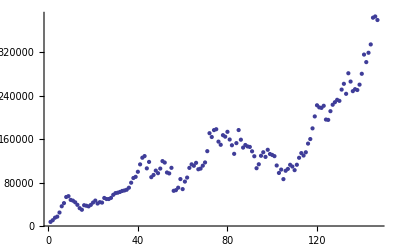

```mathematica
gr1=ListPlot[lis5]
```

◀     |     ▶

## Analisando Dados

Uma função muito útil é NonlinearRegression

```mathematica
<<NonlinearRegression`;
```

```mathematica
sol=NonlinearRegress[lis5,a+b*x+c*x*x,{a,b,c},{x}]
```

{BestFitParameters→{a→46698.5,b→122.053,c→10.298},ParameterCITable→ | Estimate | Asymptotic SE | CI
a | 46698.5 | 8987.61 | {28933.8,64463.2}
b | 122.053 | 280.369 | {-432.118,676.223}
c | 10.298 | 1.83501 | {6.67093,13.925},EstimatedVariance→1.28378×10^9,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 3 | 3.26751×10^12 | 1.08917×10^12
Error | 144 | 1.84865×10^11 | 1.28378×10^9
Uncorrected Total | 147 | 3.45237×10^12 | 
Corrected Total | 146 | 9.4258×10^11 | ,AsymptoticCorrelationMatrix→(1. | -0.869309 | 0.750398
-0.869309 | 1. | -0.968659
0.750398 | -0.968659 | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 0
Max Parameter-Effects | 0
95. % Confidence Region | 0.612283}

◀     |     ▶

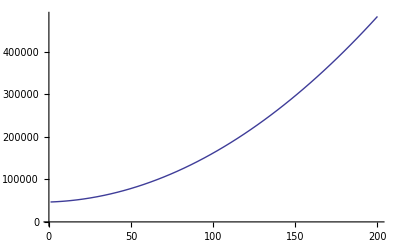

```mathematica
gr2=Plot[(a+b*x+c*x*x)/.sol[[1,2]],{x,1,200}]
```

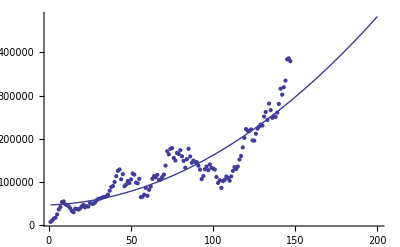

```mathematica
Show[gr1,gr2]
```

```mathematica
Export["bobo.csv",lis5]
```

```mathematica
UninstallJava[]
$AllowInternet = True
```

LinkObject::linkn: Argument LinkObject["'/Applications/Mathematica.app/SystemFiles/Links/JLink/JLink.app/Contents/MacOS/JavaApplicationStub' -init \"/tmp/m000005294091\"", 1418, 4] in LinkClose[LinkObject["'/Applications/Mathematica.app/SystemFiles/Links/JLink/JLin" … "ntents/MacOS/JavaApplicationStub' -init \"/tmp/m000005294091\"", 1418, 4]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject["659_shm", 1419, 6] in LinkClose[LinkObject["659_shm", 1419, 6]] has an invalid LinkObject number; the link may be closed.

True

```mathematica
img=Import["http://www.rc.unesp.br/igce/ceurb/basededados/imagens%20satelite/botucatu.jpg"]
```

FileFormat::nffil: File not found during FileFormat["/tmp/m000010294091/botucatu.jpg"].

Import::infer: Cannot infer format of file "botucatu.jpg".

$Failed

```mathematica
img=Import["Desktop/botucatu.jpg"]
```

-Graphics-

```mathematica
lisimg1=Flatten[img[[1,1]],1];
```

```mathematica
lisimga=lisimg1/.{x_,y_,z_}->x;
lisimgb=lisimg1/.{x_,y_,z_}->y;
lisimgc=lisimg1/.{x_,y_,z_}->z;
```

```mathematica
liscora=Sort[Tally[lisimga],#1[[1]]<#2[[1]]&];
liscorb=Sort[Tally[lisimgb],#1[[1]]<#2[[1]]&];
liscorc=Sort[Tally[lisimgc],#1[[1]]<#2[[1]]&];
```

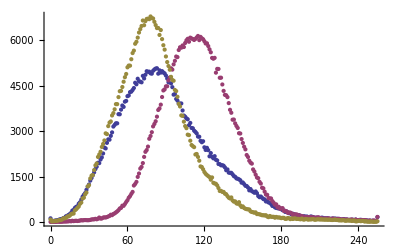

```mathematica
ListPlot[{liscora,liscorb,liscorc}]
```

```mathematica
func={{{{1./2.,0.},{0.,1./2.}},{0.,0.}},
{{{1./2.,0.},{0.,1./4.}},{0.,0.5}},
{{{1./3.,0.},{0.,1./2.}},{0.5,0.}},
{{{1./5.,0.},{0.,1./4.}},{0.3,0.1}}
};
```

```mathematica
IFS[point_]:=Module[{},
k=Random[Integer,2]+1;
func[[k,1]].point+func[[k,2]]
]
Real2Digits[d_][x_]:=Module[{lis},
lis=RealDigits[x,2,d];
Take[Prepend[lis[[1]],Table[0,{-lis[[2]]-1}]]//Flatten,{1,d}]
]
```

```mathematica
Real2Digits[5][0.45678]
```

{1,1,1,0,1}

```mathematica
lis=Take[NestList[IFS,{0.32,0.32},100000],{50000,100000}];
```

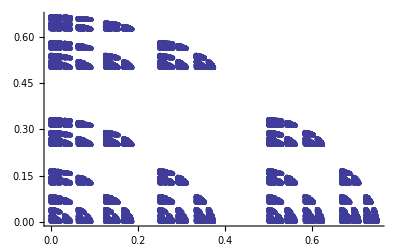

```mathematica
ListPlot[lis]
```

```mathematica
lis2=Table[{2^-k,Length[Union[Map[Real2Digits[k], lis,{2}]]]},{k,1,10}];
```

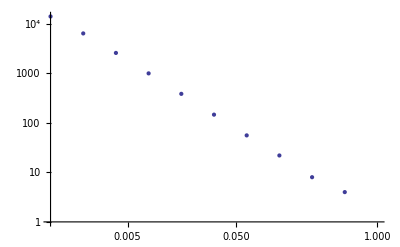

```mathematica
gr1=ListLogLogPlot[lis2]
```

```mathematica
lis3=lis2[[Range[1,7]]]
```

{{1/2,4},{1/4,8},{1/8,22},{1/16,56},{1/32,147},{1/64,387},{1/128,1003}}

```mathematica
exp1=NonlinearRegress[lis3,a*x^b,{a,b},{x}]
```

{BestFitParameters→{a→1.24367,b→-1.37942},ParameterCITable→ | Estimate | Asymptotic SE | CI
a | 1.24367 | 0.0176548 | {1.19829,1.28906}
b | -1.37942 | 0.00299348 | {-1.38711,-1.37172},EstimatedVariance→1.03393,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 2 | 1.18108×10^6 | 590541.
Error | 5 | 5.16966 | 1.03393
Uncorrected Total | 7 | 1.18109×10^6 | 
Corrected Total | 6 | 802926. | ,AsymptoticCorrelationMatrix→(1. | 0.997826
0.997826 | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 0.00262753
Max Parameter-Effects | 0.303297
95. % Confidence Region | 0.415725}

```mathematica
exp2=a*x^b/.{a->1.243674632267061,b->-1.3794157703723047}
```

1.24367/x^1.37942

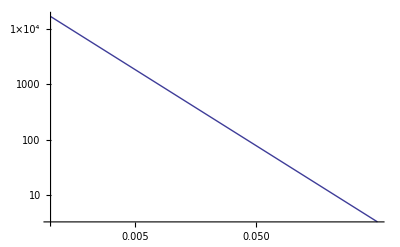

```mathematica
gr2=LogLogPlot[exp2,{x,0.001,0.5}]
```

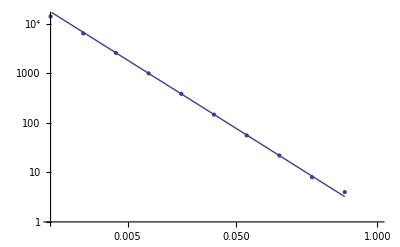

```mathematica
Show[gr1,gr2]
```